```mathematica
SetOptions[{Plot, ListPlot,LogLogPlot,LogLinearPlot,LogPlot},GridLines->Automatic];
```

π[x] – number of primes numbers ≤ x, aka prime counting function.

### Prime numbers

```mathematica
Prime[ Range[30]]
```

```mathematica
Accumulate[{a,b,c,d}]
```

```mathematica
Accumulate[Prime[ Range[30]]]
```

```mathematica
primes1K=Prime[ Range[1000]];
```

```mathematica
{primes1K, Accumulate[primes1K^1]}ᵀ
```

```mathematica
ListPlot[{primes1K, Accumulate[primes1K^1]}ᵀ]
```

```mathematica
ListPlot[{primes1K, Accumulate[primes1K^-1]}ᵀ]
```

```mathematica
{primes1K, Accumulate[primes1K^0]}ᵀ
```

```mathematica
ListPlot[{primes1K, Accumulate[primes1K^0]}ᵀ]
```

```mathematica
Accumulate[primes1K^0]==Range[Length[primes1K]]
```

### Let’s crack primes counting π function

Number of prime numbers ≤ x

```mathematica
primes30=Prime[Range[30]];
```

```mathematica
gl=ListPlot[{primes30, Accumulate[primes30^0]}ᵀ,PlotStyle->Orange,Joined->True]
```

```mathematica
primes=N[Prime[ Range[3002195]]];
primePi = Accumulate[primes^0];
```

But we have already PrimePi function in Mathematica

```mathematica
PrimePi[2] (* {2} *)
```

```mathematica
PrimePi[10] (* {2,3,5,7} *)
```

```mathematica
PrimePi[600000000000]
```

```mathematica
g=Plot[PrimePi[x],{x,0,70},PlotPoints->200]
```

```mathematica
Show[g,gl]
```

```mathematica
Plot[PrimePi[x]/x,{x,2,1000000},PlotRange->{Automatic,{0,Automatic}}]
```

8 % of numbers are prime in [1, 1 000 000]

```mathematica
f[x_]:= PrimePi[x]/x;
Plot[f[Exp[lx]],{lx,2,30}]
```

```mathematica
f[x_]:= PrimePi[x]/(x /Log[x]);
Plot[f[Exp[lx]],{lx,2,30}]
```

Theorem: lim_(x→ ∞) PrimePi[x]/(x /Log[x]) = 1

```mathematica
f[x_,a_]:= PrimePi[x]-x/Log[x]^a; (* <- wrong idea *)
```

```mathematica
f[x_,a_]:= PrimePi[x]-x/(Log[x]-a);
Manipulate[
Plot[f[x,a],{x,2,50000000}],
{{a,1.086},0.5,1.5}
]
```

```mathematica
f[x_,a_]:= (PrimePi[x]-x/(Log[x]-a));
Manipulate[
Plot[{f[x,a],0.01b x^c },{x,2,10000000},PlotPoints->50],
{{a,1.05},0.9,1.2},
{{b,2.1},0.001,4},
{{c,0.67},0.1,0.8}
]
```

```mathematica
f[x_,a_,b_,c_]:= (PrimePi[x]-x/(Log[x]-a)-0.01b x^c )/Sqrt[x];
Manipulate[
Plot[f[x,a,b,c],{x,2,10000000},PlotPoints->50],
{{a,1.05},0.9,1.2},
{{b,2.1},0.001,4},
{{c,0.67},0.1,0.8}
]
```

```mathematica
f[x_,a_,b_,c_]:= (PrimePi[x]-x/(Log[x]-a)-0.01b x^c +40)/Sqrt[x];
Manipulate[
Plot[f[x,a,b,c],{x,2,10000000},PlotPoints->50,  AspectRatio->1/4],
{{a,1.05},0.9,1.2},
{{b,2.1},0.001,4},
{{c,0.67},0.1,0.8}
]
```

```mathematica
(π-x/(Log[x]-1.05)-0.021 x^0.67+40)/Sqrt[x]==noise
```

```mathematica
Solve[
(pi-n / (Log[n]-1.05)-0.021 n^0.67 + 40) / Sqrt[n]==noise,
pi
]//Expand
```

This is bad approximation. It' s just for illustration

### Library

```mathematica
QRange[k_,nSteps_,prefix_]:=DeleteDuplicates[Sort[Join[Range[prefix], Round[Exp[# Log[k]/nSteps]&/@Range[nSteps]]]]
] ;
QRange[k_,nSteps_]:=QRange[k,nSteps,100] ;
```

```mathematica
QRange[1000,100,5]
```

```mathematica
ListQPart[l_,nSteps_,prefix_]:=l⟦QRange[Length[l],nSteps,prefix]⟧;
ListQPart[l_,nSteps_]:=ListQPart[l,nSteps,100];
```

```mathematica
CatXYs[l1_,l2_]:={#⟦1,1⟧,#⟦1,2⟧,#⟦2,2⟧}&/@({l1,l2}ᵀ);
CatXYs[ls_]:=(Flatten[{Sequence[#⟦1,1⟧], (#⟦2⟧&/@#)}])&/@(lsᵀ)
```

### Find coeffs by minimizing noise ATTEMPT0

```mathematica
expr=n/(-a+Log[n])+c n^d +e+√n (noise-b);
```

```mathematica
Clear[n];
Solve[pi==expr,noise]//FullSimplify
```

```mathematica
Noise[n_]:=(e-b √n+c n^d-PrimePi[n]+n/(-a+Log[n]))/(√n);
```

```mathematica
loss=Mean@(Noise[#]^2&/@(10+QRange[500000000000,2000,5]));
solution=NMinimize[
loss,
{{a,0.9,1.2},{b,-0.5,0.5},{c,0.0002, 0.1},{d,0.2,0.76},{e,-4,4}},
Method->"SimulatedAnnealing"
]
```

```mathematica
PrimePiMy[n_]:=Evaluate[expr/.solution[[2]]/.{noise->0}];
PrimePiMy[n]
```

```mathematica
ListPlot[{Log[#],(PrimePiMy[#]- PrimePi[#])/Sqrt[#] Log[#] }&/@(2+QRange[5000000000000,5000,100])]
```

### Find coeffs by minimizing noise ATTEMPT1

```mathematica
expr=n/(-a+Log[n])+c n^d +e+√n (noise-b);
```

```mathematica
expr=n/(-a+Log[n])+c n^d+e+(√n (noise-b))/Log[n];
```

```mathematica
Clear[n];
Solve[pi==expr,noise]//FullSimplify
```

```mathematica
Noise[n_]:=(Log[n] (e+c n^d-PrimePi[n]-(b √n)/Log[n]+n/(-a+Log[n])))/(√n);
```

```mathematica
loss=Mean@(Noise[#]^2&/@(10+QRange[500000000000,2000,5]));
solution=NMinimize[
loss,
{{a,0.9,1.2},{b,-0.5,0.5},{c,0.0002, 0.1},{d,0.2,0.76},{e,-4,4}},
Method->"SimulatedAnnealing"
]
```

```mathematica
PrimePiMy[n_]:=Evaluate[expr/.solution[[2]]/.{noise->0}];
PrimePiMy[n]
```

```mathematica
ListPlot[{Log[#],(PrimePiMy[#]- PrimePi[#])/Sqrt[#] Log[#] }&/@(2+QRange[5000000000000,5000,100])]
```

### Find coeffs by minimizing noise ATTEMPT2

```mathematica
expr=n/(-a+Log[n])+(b3 n)/(Log[n])^3+(b4 n)/(Log[n])^4+(b5 n)/(Log[n])^5+(√n (noise+d))/Log[n]+e;
```

```mathematica
Clear[n];
Solve[pi==expr,noise]
```

```mathematica
Noise[n_]:=(Log[n] (e-PrimePi[n]+(b5 n)/Log[n]^5+(b4 n)/Log[n]^4+(b3 n)/Log[n]^3+(d √n)/Log[n]+n/(-a+Log[n])))/(√n);
```

```mathematica
loss=Mean@(Noise[#]^2&/@(2+QRange[500000000000,2000,5]));
solution=NMinimize[
loss,
{{a,0.95,1.1},{b3,-1,1},{b4,-10,10},{b5,-10,10},{d,-1.5,1.5},{e,-3,3}},
Method->"SimulatedAnnealing"
]
```

```mathematica
PrimePiMy[n_]:=Evaluate[expr/.solution[[2]]/.{noise->0}];
PrimePiMy[n]
```

```mathematica
ListPlot[{Log[#],(PrimePiMy[#]- PrimePi[#])/Sqrt[#] Log[#]}&/@(2+QRange[500000000000,5000,100]),AspectRatio->1/4,AxesLabel->{"Log[x]","noise"},AxesOrigin->{0,-0.5}]
```

```mathematica
ListPlot[{Log[#],(PrimePiMy[#]- PrimePi[#])/Sqrt[#] Log[#]}&/@(2+QRange[500000000000,5000,100]),AspectRatio->1/4,AxesOrigin->{0,-0.5}]
```

```mathematica
Series[1/(-1.005182+Log[n])-28.7385/Log[n]^5+13.1891/Log[n]^4+0.62466/Log[n]^3,{Log[n],∞,6}]//Expand
```

### Find coeffs by minimizing noise ATTEMPT3

```mathematica
expr=n/(-a+Log[n])+(b3 n)/(Log[n])^3+(b4 n)/(Log[n])^4+(b5 n)/(Log[n])^5+(√n (noise+d))/Log[n]+e;
```

```mathematica
expr=n/Log[n](1+b1/(Log[n])^1+b2/(Log[n])^2+b3/(Log[n])^3+b4/(Log[n])^4)+(√n (noise+d))/Log[n]+e;
```

```mathematica
Clear[n];
Solve[pi==expr,noise]
```

```mathematica
Noise[n_]:=d+Log[n]/(√n) (
e-PrimePi[n]+n/Log[n] (1+b4/(Log[n])^4+b3/(Log[n])^3+b2/(Log[n])^2+b1/Log[n])
);
```

```mathematica
loss=Mean@(Noise[#]^2&/@(2+QRange[500000000000,4000,5]));
solution=NMinimize[
loss,
{b1,b2,b3,b4,d,e},
Method->"SimulatedAnnealing"
]
```

```mathematica
PrimePiMy[n_]:=Evaluate[expr/.solution[[2]]/.{noise->0}];
PrimePiMy[n]
```

```mathematica
ListPlot[
{Log[#],(PrimePiMy[#]- PrimePi[#])/Sqrt[#] Log[#]}&/@(2+QRange[5000000000000,5000,100]),
AspectRatio->1/4,ImageSize->Large
]
```

### P sum of 1, aka π(n) function – approximating by Li(n)

```mathematica
∫_2^y 1/Log[x] ⅆx
```

```mathematica
∫_0^y (1/Log[x]-1/(x-1))ⅆx
```

```mathematica
Assuming[{x>0},Series[LogIntegral[x],{x,∞,5}]]//Normal//Expand
```

```mathematica
Assuming[{x>0},Series[LogIntegral[x]/x,{x,∞,5}]]//Normal//Expand
```

```mathematica
Assuming[{x>0},Series[LogIntegral[Exp[x]]/Exp[x],{x,∞,16}]]//Normal//Expand
```

```mathematica
PrimePiMy[x]
```

```mathematica
Nn[x_]:=Sqrt[x]/Log[x];
f0[x_]:= 1/Nn[x](PrimePi[x]-x/(Log[x]-1.05));
f1[x_]:= 1/Nn[x](PrimePi[x]-PrimePiMy[x]);
h[x_]:=1/Nn[x](PrimePi[x]-LogIntegral[x]+1/2LogIntegral[Sqrt[x]]);
LogLinearPlot[
{f0[x],f1[x], h[x]},
{x,2,500000000},PlotPoints->50,  AspectRatio->1/3,ImageSize->Large
]
```

### Riemann formula for π (n) based on Li (n)

```mathematica
R[x_,n_]:=∑_(i=1)^n MoebiusMu[i]/i LogIntegral[Exp[Log[x]/i]];
```

```mathematica
R[x,17]
```

```mathematica
PrimePiLIApprox[x_,n_]:=R[x,n] + 1/π ArcTan[π/Log[x]]-1/Log[x]
```

```mathematica
LogLogPlot[-1/π ArcTan[π/x]+1/x,{x,2,10000},PlotRange->{Automatic,{0,Automatic}}]
```

```mathematica
Nn[x_]:=Log[x]/Sqrt[x];
LogLinearPlot[{
Nn[x](PrimePi[x]-x/(Log[x]-1.05)),
Nn[x](PrimePi[x]-PrimePiMy[x]),
Nn[x](PrimePi[x]-LogIntegral[x]+1/2 LogIntegral[Sqrt[x]]),
Nn[x] (PrimePi[x]-PrimePiLIApprox[x,3])
},{x,1,1000000000}]
```

```mathematica
PrimePiMy[x]
```

```mathematica
Nn[x_]:=Log[x]/Sqrt[x];
LogLinearPlot[{
Nn[x](PrimePiMy[x]-PrimePiLIApprox[x,150])
},{x,1,10000000000000},PlotRange->{Automatic,{-0.5,0.5}}
]
```

### Takeaways

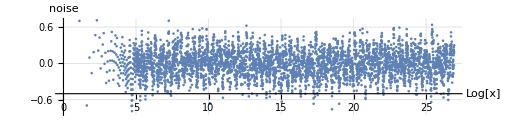
Take aways
1)  π[x] ~x/Log[x],  and    lim_(x→ ∞)  π[x] /x/Log[x]=1  
2) It is easy to get The Noise exploring PrimePi function :  π[x]-x/Log[x]-(b_1 x)/Log[x]^2-(b_2 x)/Log[x]^3-...
We came to
π[x] =x/Log[x](1+b_1/Log[x]+b_2/Log[x]^2+b_3/Log[x]^3+...)+(√x)/Log[x]noise_1[x]
where noise_1[x] is (as function of Log[x])
-Graphics-
3) NMinimize could be uses to fit coefficients {b_1,b_2,...} of approx formulas. 
And simple check for extrapolation shows correctness of the formula.
4) Good PrimePi approximation (Riemann) is based on LogIntegral function. 
li[x]=∫_0^x 1/Log[t]ⅆt
How can one come to the idea of estimating |π[x] - li[x]|? It is poorly covered on the Internet.

It looks like

π[x]= li[x]+(√x)/Log[x]noise
but more precise fact (not proven here) is

π[x]= R[x]+ η[x] +(√x)/Log[x]noise,
where
    R[x]= li[x]-1/2 li[x^(1/2)]-1/3 li[x^(1/3)]-1/5 li[x^(1/5)]+1/6 li[x^(1/6)]+..;
    η[x]= 1/π arctan(π/Log[x])-1/Log[x]=O[1/Log[x]^2].

5)  (√x)/Log[x]noise<C √x Log[x] is equivalent to Riemann hypothesis.

noise<C Log[x]^2

Riemann hypothesis == non trivial zeros of ζ-function lay on line Re[z]==1/2.
ζ[z] := analytic continuation of ζ[z]=∑_(k=1)^∞ 1/k^z.